```mathematica
GCDBinario[a_,b_]:=(Module[{d,d0,x,A,B,moda,modb},
x=Sort[{a,b}];A=x[[2]];B=x[[1]];
moda=Mod[A,2];modb=Mod[B,2];
Which[a==b ,Return[a],And[moda==0,modb==0],Return[2*GCDBinario[Quotient[A,2],Quotient[B,2]]],And[moda==0,modb==1],Return[GCDBinario[Quotient[A,2],B]],And[moda==1,modb==0],Return[GCDBinario[A,Quotient[B,2]]],And[moda==1,modb==1],Return[GCDBinario[Quotient[(A-B),2],B]]
]
]
)
```

{0.,0.}

{0.015625,0.}

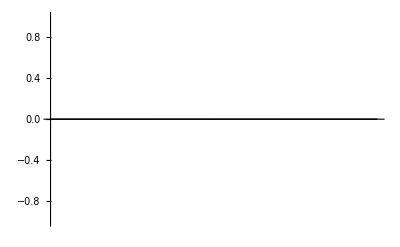

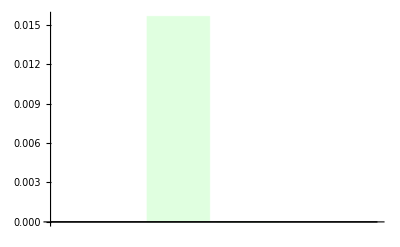

```mathematica
a=Random[Integer,{10,10^5}];
b=Random[Integer,{10,10^5}];
c=Random[Integer,{10^99,10^100}];
d=Random[Integer,{10^99,10^100}];
t1={Part[Timing[GCDBinario[a,b]],1],Part[Timing[GCD[a,b]],1]}
t2={Part[Timing[GCDBinario[c,d]],1],Part[Timing[GCD[c,d]],1]}
BarChart[t1,ChartStyle->{LightGreen}]
BarChart[t2,ChartStyle->{LightGreen}]
```